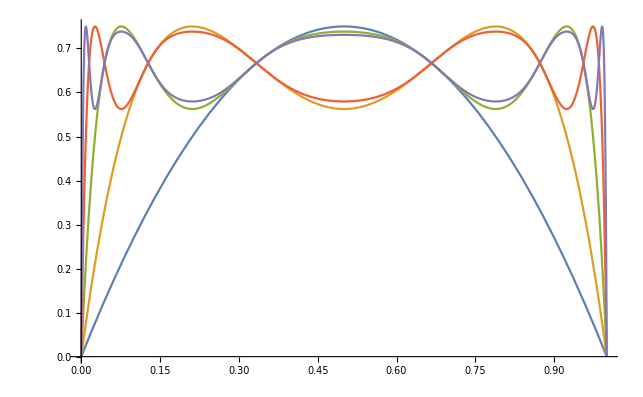

```mathematica
funcs=RecurrenceTable[{x[n+1]==r x[n] (1-x[n]),x[0]==x0},x,{n,1,5}];
Plot[funcs/.r->3,{x0,0,1},Evaluated->True,PlotRange->All]
```

```mathematica
Manipulate[Plot[funcs/.r->rr,{x0,0,1},Evaluated->True,PlotRange->All,ImageSize->500,PlotLabel->Row[{"r = ",rr}],LabelStyle->18],{rr,-2,4,.01}]
```